```mathematica
deq1=x'[t]==-2x[t]+y[t]+Exp[-t]
deq2=y'[t]==x[t]-2y[t]+3t
```

x'[t]==ⅇ^-t-2 x[t]+y[t]

y'[t]==3 t+x[t]-2 y[t]

```mathematica
DSolve[{deq1,deq2},{x[t],y[t]},t]
```

{{x[t]→1/4 ⅇ^(-3 t) (1+ⅇ^(2 t)) (ⅇ^(2 t)/2-3 ⅇ^(3 t) (-1/9+t/3)+3 ⅇ^t (-1+t)+t)+1/4 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (-ⅇ^(2 t)/2+3 ⅇ^(3 t) (-1/9+t/3)+3 ⅇ^t (-1+t)+t)+1/2 ⅇ^(-3 t) (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) C[2],y[t]→1/4 ⅇ^(-3 t) (-1+ⅇ^(2 t)) (ⅇ^(2 t)/2-3 ⅇ^(3 t) (-1/9+t/3)+3 ⅇ^t (-1+t)+t)+1/4 ⅇ^(-3 t) (1+ⅇ^(2 t)) (-ⅇ^(2 t)/2+3 ⅇ^(3 t) (-1/9+t/3)+3 ⅇ^t (-1+t)+t)+1/2 ⅇ^(-3 t) (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-3 t) (1+ⅇ^(2 t)) C[2]}}

```mathematica
DSolve[{deq1,deq2,x[0]==0,y[0]==3},{x1[t],x2[t]},t]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[SuperscriptBox[TrueTrue.

DSolve[{x'[t]==ⅇ^-t-2 x[t]+y[t],y'[t]==3 t+x[t]-2 y[t],True,True},{x1[t],x2[t]},t]

```mathematica
Solve[{-2x[t]+y[t]+Exp[-t]==0,x[t]-2y[t]+3t==0},{x[t],y[t]}]
```

{{x[t]→1/3 ⅇ^-t (2+3 ⅇ^t t),y[t]→ⅇ^-t/3+2 t}}

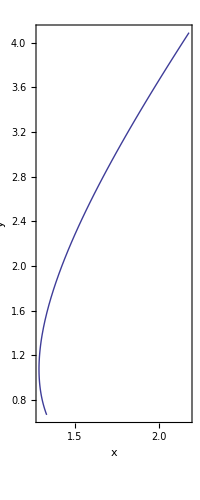

```mathematica
steady=ParametricPlot[{1/3 ⅇ^-t (4+3 ⅇ^t t),2/3 ⅇ^-t (1+3 ⅇ^t t)},{t,0,2}, Frame-> True,Axes->False, FrameLabel->{"x","y"}]
```

```mathematica
dek1=x'[t]==-5x[t]+2y[t]+x[t]y[t]
dek2=y'[t]==x[t]+y[t]-4y[t]x[t]
```

x'[t]==-5 x[t]+2 y[t]+x[t] y[t]

y'[t]==x[t]+y[t]-4 x[t] y[t]

```mathematica
DSolve[{dek1,dek2},{x[t],y[t]},t]
```

DSolve[{x'[t]==-5 x[t]+2 y[t]+x[t] y[t],y'[t]==x[t]+y[t]-4 x[t] y[t]},{x[t],y[t]},t]

```mathematica
Clear[f1,f2]
```

```mathematica
f1[x1_,x2_]=-5x1+2x2+x1 x2
f2[x1_,x2_]=x1+x2-4x2 x1
```

-5 x1+2 x2+x1 x2

x1+x2-4 x1 x2

```mathematica
Solve[{f1[x1,x2]==0,f2[x1,x2]==0},{x1,x2}]
```

{{x1→0,x2→0},{x1→7/19,x2→7/9}}

```mathematica
field=VectorPlot[{f1[x1,x2],f2[x1,x2]},{x1,-1,1},{x2,-1,1},Frame->True]
```